# Sistemas de ecuaciones en diferencias

## Ejemplo I

Punto de equilibrio no trivial:

```mathematica
N[ArcTanh[3/4]/2]
```

0.486478

Matriz Jacobiana:

```mathematica
j1[x_]:=({{1/2+(1-Tanh[x])-x*Sech[x]^2, 1/2}, {1/4, 1/2}})
```

Eigenvalores en el origen:

```mathematica
N[Eigenvalues[j1[0]]]
```

{1.61237,0.387628}

Eigenvalores en el equilibio no trivial:

```mathematica
N[Eigenvalues[j1[ArcTanh[3/4]]]]
```

{0.776467,0.0478657}

Trayectoria con condiciones iniciales cercanas al origen:

```mathematica
sist1=RecurrenceTable[{y[k+1]==y[k]/2+z[k]/2+y[k]*(1-Tanh[y[k]]),z[k+1]==y[k]/4+z[k]/2,y[1]==0.00001,z[1]==0.00001},{y,z},{k,1,100}];
```

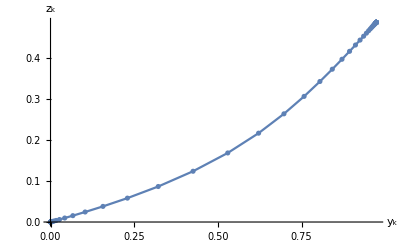

```mathematica
lp1=ListPlot[sist1,PlotRange->All,Joined->True,Mesh->All,AxesLabel->{Subscript[y,k],Subscript[z,k]}]
```

```mathematica
Export["ex1phsp-dbifs.jpg",lp1,CompressionLevel->0]
```

ex1phsp-dbifs.jpg

Componentes de la solución:

```mathematica
s1y=Table[{k,sist1[[k]][[1]]},{k,1,100}];
s2y=Table[{k,sist1[[k]][[2]]},{k,1,100}];
```

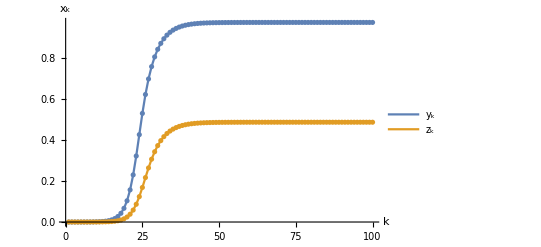

```mathematica
lp2=ListPlot[{s1y,s2y},AxesLabel->{k,Subscript[x,k]},Joined->True,Mesh->All,PlotLegends->{Subscript[y,k],Subscript[z,k]}]
```

```mathematica
Export["ex1sols-dbifs.jpg",lp2,CompressionLevel->0]
```

ex1sols-dbifs.jpg

## Ejemplo II

Caso :

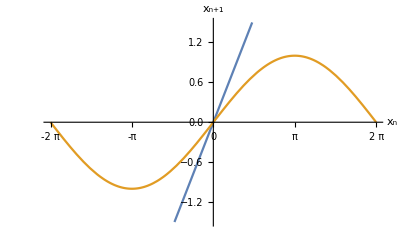

```mathematica
p1=Plot[{x,Sin[x/2]},{x,-2*Pi,2*Pi},AxesLabel->{Subscript[x,n],Subscript[x,n+1]},Ticks->{{-2*Pi,-3*Pi/2,-Pi,-Pi/2,0,Pi/2,Pi,3*Pi/2,2*Pi},Automatic},PlotRange->{{-2*Pi,2*Pi},{-1.5,1.5}}]
```

```mathematica
Export["fde-suppitch-prec-cobweb.jpg",p1,CompressionLevel->0]
```

fde-suppitch-prec-cobweb.jpg

```mathematica
spb=RecurrenceTable[{x[n+1]==Sin[x[n]/2],x[1]==1/10},x,{n,1,20}];
```

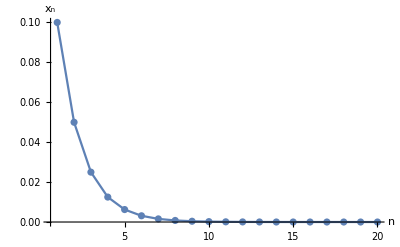

```mathematica
lp3=ListPlot[spb,AxesLabel->{n,Subscript[x,n]},Joined->True,Mesh->All,PlotRange->All]
```

```mathematica
Export["fde-suppitch-prec-sol.jpg",lp3,CompressionLevel->0]
```

fde-suppitch-prec-sol.jpg

Cerca del punto de equilibrio, la solución decrece exponencialmente a cero, como se ve en la gráfica log-lineal:

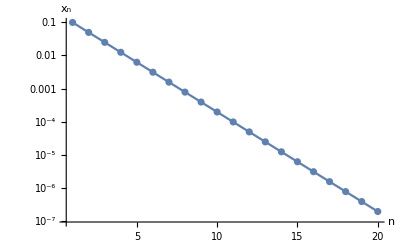

```mathematica
lp4=ListPlot[spb,AxesLabel->{n,Subscript[x,n]},Joined->True,Mesh->All,PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
Export["fde-suppitch-prec-sollog.jpg",lp4,CompressionLevel->0]
```

fde-suppitch-prec-sollog.jpg

Caso :
Lo vimos anteriormente y usando el cobweb plot determinamos que era estable, aunque su eigenvalor es :

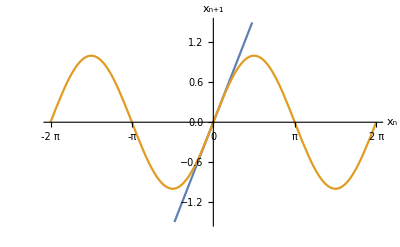

```mathematica
p2=Plot[{x,Sin[x]},{x,-2*Pi,2*Pi},AxesLabel->{Subscript[x,n],Subscript[x,n+1]},Ticks->{{-2*Pi,-3*Pi/2,-Pi,-Pi/2,0,Pi/2,Pi,3*Pi/2,2*Pi},Automatic},PlotRange->{{-2*Pi,2*Pi},{-1.5,1.5}}]
```

```mathematica
Export["fde-suppitch-c-cobweb.jpg",p2,CompressionLevel->0]
```

fde-suppitch-c-cobweb.jpg

```mathematica
sb=RecurrenceTable[{x[n+1]==Sin[x[n]],x[1]==1},x,{n,1,1000}];
```

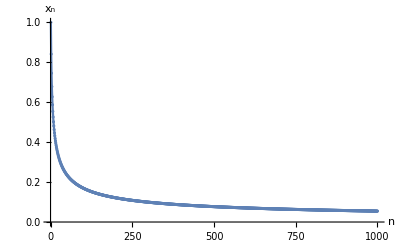

```mathematica
lp5=ListPlot[sb,AxesLabel->{n,Subscript[x,n]},Joined->True,Mesh->All,PlotRange->All]
```

```mathematica
Export["fde-suppitch-c-sol.jpg",lp5,CompressionLevel->0]
```

fde-suppitch-c-sol.jpg

Las soluciones decaen al punto de equilibrio también, pero lo hacen como una ley de potencias, como es evidente con la gráfica log-log:

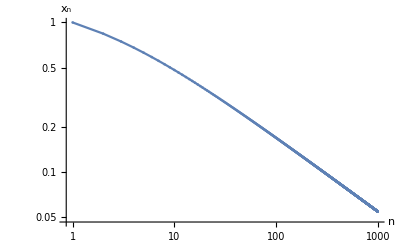

```mathematica
lp6=ListPlot[sb,AxesLabel->{n,Subscript[x,n]},Joined->True,Mesh->All,PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

```mathematica
Export["fde-suppitch-c-solloglog.jpg",lp6,CompressionLevel->0]
```

fde-suppitch-c-solloglog.jpg

Caso :

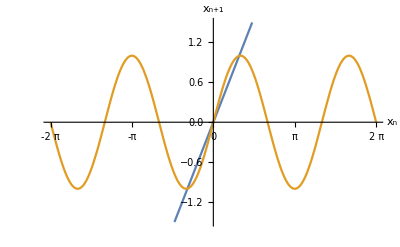

```mathematica
p3=Plot[{x,Sin[3*x/2]},{x,-2*Pi,2*Pi},AxesLabel->{Subscript[x,n],Subscript[x,n+1]},Ticks->{{-2*Pi,-3*Pi/2,-Pi,-Pi/2,0,Pi/2,Pi,3*Pi/2,2*Pi},Automatic},PlotRange->{{-2*Pi,2*Pi},{-1.5,1.5}}]
```

```mathematica
Export["fde-suppitch-posc-cobweb.jpg",p3,CompressionLevel->0]
```

fde-suppitch-posc-cobweb.jpg

Surgen dos nuevos puntos de equilibrio. Con condiciones iniciales cerca del equilibrio estable, las soluciones se alejan y convergen a los nuevos puntos de equilibrio, dependiendo del valor preciso de la condición inicial:

```mathematica
spsb=RecurrenceTable[{x[n+1]==Sin[3*x[n]/2],x[1]==0.00001},x,{n,1,50}];
```

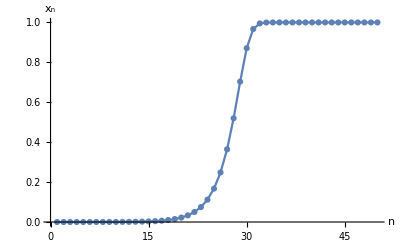

```mathematica
lp7=ListPlot[spsb,Joined->True,Mesh->All,AxesLabel->{n,Subscript[x,n]},PlotRange->All]
```

```mathematica
Export["fde-suppitch-posc-sol.jpg",lp7,CompressionLevel->0]
```

fde-suppitch-posc-sol.jpg

```mathematica
spsb2=RecurrenceTable[{x[n+1]==Sin[3*x[n]/2],x[1]==-0.00001},x,{n,1,50}];
```

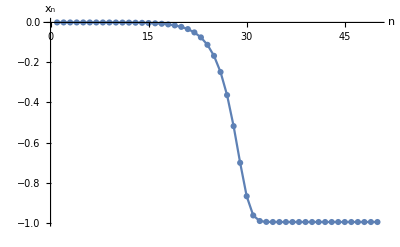

```mathematica
lp8=ListPlot[spsb2,Joined->True,Mesh->All,AxesLabel->{n,Subscript[x,n]},PlotRange->All]
```

```mathematica
Export["fde-suppitch-posc-soln.jpg",lp8,CompressionLevel->0]
```

fde-suppitch-posc-soln.jpg

```mathematica
stst=Table[{w,x/.FindRoot[x==Sin[w*x],{x,1}]},{w,1,2,0.00001}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Se trata de una bifurcación de tridente supercrítica. Viendo qué pasa si seguimos aumentando  después de la bifurcación, observamos que el eigenvalor se vuelve negativo eventualmente:

```mathematica
eigs=Table[{stst[[i]][[1]],stst[[i]][[1]]*Cos[stst[[i]][[1]]*stst[[i]][[2]]]},{i,1,1001}];
```

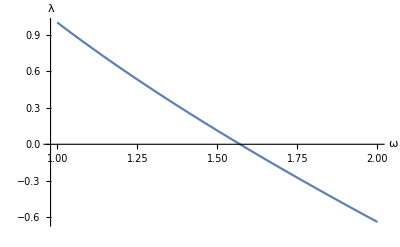

```mathematica
lp9=ListPlot[eigs,Joined->True,AxesLabel->{ω,λ}]
```

```mathematica
Export["fde-suppitch-eigspec.jpg",lp9,CompressionLevel->0]
```

fde-suppitch-eigspec.jpg

Esto indica que las soluciones se vuelven oscilatorias:

```mathematica
sinex=RecurrenceTable[{x[n+1]==Sin[x[n]*1.9],x[1]==0.94},x,{n,1,15}];
```

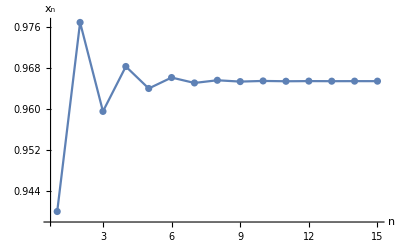

```mathematica
lp10=ListPlot[sinex,Joined->True,Mesh->All,AxesLabel->{n,Subscript[x,n]},PlotRange->All]
```

```mathematica
Export["fde-suppitch-posc-solosci.jpg",lp10,CompressionLevel->0]
```

fde-suppitch-posc-solosci.jpg

Graficando el diagrama de bifurcación de manera numérica, observamos que muestra la forma típica de una bifurcación de tridente supercrítica:

```mathematica
stst2=Table[{w,x/.FindRoot[x==Sin[w*x],{x,-1}]},{w,1,2,0.00001}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
sh1=Show[Plot[0,{x,0,1},PlotStyle->Thick,AxesLabel->{ω,SuperStar[x]},PlotRange->{{0,2},{-1.1,1.1}}],ListPlot[stst,PlotStyle->{Thick,Red},Joined->True,PlotRange->All],ListPlot[stst2,PlotStyle->{Thick,Red},Joined->True,PlotRange->All],Plot[0,{x,1,2},PlotStyle->{Thick,Dashed}]]
```

-Graphics-

```mathematica
Export["fde-suppitch-bifdiag.jpg",sh1,CompressionLevel->0]
```

fde-suppitch-bifdiag.jpg